## Some Examples for Tiger of the sorts of things one could do:

```mathematica
(* Comments are in these *)
```

```mathematica
(* Tip: You are looking at a notebook, which is just a text file containing the things you want to do, or have done in the past, or results Mathematica has given you.
 But the brains (the thought, the state, the memory) is in some thing called "The Kernel" which is a process going on in the background. Sometimes if you mess up your state you need to kill the kernal and re-start a new one. You do this from the bottom of the "Evaluation" part of the menu (sub-options "quit kernel" or "startKernel -> Local".
When you presss "shift-enter" in the notebook, the current statement is passed to the kernel which thinks about it and then gives you an answer back when it is done.  
*)
```

```mathematica
someDifferentialEquations = {
D[x[t],t] == 5x[t]-3 y[t],  (* Note that equations have == not = in them.  = is used for assignment *)
D[y[t],t] == -6x[t]+2 y[t]
}
```

{x'[t]==5 x[t]-3 y[t],y'[t]==-6 x[t]+2 y[t]}

```mathematica
someInitialConditions = {
x[0]==1,
y[0]==1/2
}
```

{x[0]==1,y[0]==1/2}

```mathematica
(* Now solve the above ANALYTICALLY *)
```

```mathematica
analyticSoln = DSolve[Join[someDifferentialEquations , someInitialConditions],{x[t],y[t]},{t,0,1}]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(9 t)),y[t]→ⅇ^-t-ⅇ^(8 t)/2}}

```mathematica
(* Mathematica has given us the answer above in terms of a list of substitutions. Actually the above is a list of lists since it has form {{}} not the form {}. This is because there could hae been two solutions, in which case it might have given us {{onesoln},{secondSoln}}.  By a "substitition" I mean that the above has some right-pointing arrows in it, which is what mathematica calls substitutions. Before plotting the answer, let me show you what they are:
```

```mathematica
{5,6,7,8,9}  (* This is not being substituted)
```

```mathematica
{5,6,7,8,9}/.{6->moo}  (* Here we are substituting moo in place of 6 *)
```

{5,moo,7,8,9}

```mathematica
{x,y,z,x^2,y^2,z^2}/.{x->a}    (* Here we are changing x to a.  Note that x and x^2 are BOTH affected.*)
```

{a,y,z,a^2,y^2,z^2}

```mathematica
{x,y,z,x^2,y^2,z^2}/.{x^2->a^2}    (* Here we are changing x^2 to a^2.  Note that x is NOT affected.*)
```

{x,y,z,a^2,y^2,z^2}

```mathematica
{x,y,z,x^2,y^2,z^2}/.{x->3,y->4}    (* Here we are changing more than one thing simultaneously.*)
```

{3,4,z,9,16,z^2}

```mathematica
{x,y,z,x^2,y^2,z^2}/.{x->3,y->4} /. {16-> sixteen}    (* Here we chaining substitutions together*)
```

{3,4,z,9,sixteen,z^2}

```mathematica
(* Lets get part of a list.  Note the indexing counts from 1 not from 0. *)
{cat,dog,cow,flea}[[3]]
```

cow

```mathematica
(* Nonetheless, you can use index 0 to get the "head" of an object, i.e. it's type.  This confuses some newcomers. *)
{cat,dog,cow,flea}[[0]]
```

List

```mathematica
(* Everything has a "head", not just lists: *)
(f+g)[[0]]
```

Plus

```mathematica
(* OK putting all those tips together, let us extract the required substitution from our answer, and then plot it: *)
```

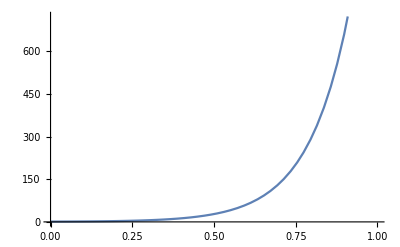

```mathematica
Plot[x[t] /. analyticSoln[[1]],{t,0,1}]
```

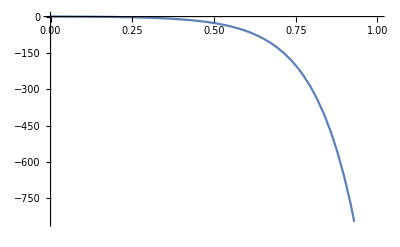

```mathematica
Plot[y[t] /. analyticSoln[[1]],{t,0,1}]
```

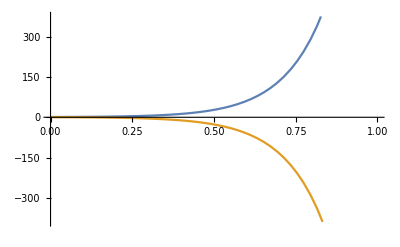

```mathematica
(* Both plots on same axis*) 
Plot[{ x[t] /. analyticSoln[[1]], y[t] /. analyticSoln[[1]]},{t,0,1}]
```

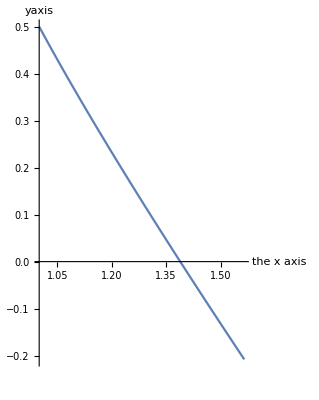

```mathematica
(* What about x against y?*) ParametricPlot[{x[t],y[t]} /. analyticSoln[[1]],{t,0,.1},AxesLabel->{"the x axis","yaxis"}]
```

```mathematica
(* What if the equations were too complicated to allow an ANALYTIC solution? Then we would instead ask for a NUMERICAL solution: *)
```

```mathematica
numericalSolution = NDSolve[Join[someDifferentialEquations , someInitialConditions],{x[t],y[t]},{t,0,1}] (* note "NDSolve" not "DSolve" *)
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
(* Plot same way as before *)
```

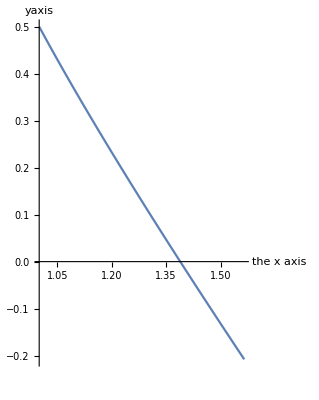

```mathematica
(* What about x against y?*) ParametricPlot[{x[t],y[t]} /. numericalSolution[[1]],{t,0,.1},AxesLabel->{"the x axis","yaxis"}]
```